```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/610nm.dat"]
```

{{1.16196,0.320996},{1.1485,0.314007},{1.13288,0.312692},{1.11879,0.286832},{1.10986,0.253944},{1.10188,0.219698},{1.0953,0.203675},{1.09118,0.206119},{1.08898,0.232619},{1.08844,0.266739},{1.08969,0.295799},{1.094,0.313715},{1.09832,0.313204},{1.10319,0.32671},{1.11502,0.322591},{1.13408,0.335186},{1.14571,0.328368},{1.16039,0.326927},{1.17699,0.330454},{1.19764,0.326999},{1.21871,0.317581},{1.24216,0.320198},{1.26543,0.324472},{1.29691,0.312326},{1.32536,0.300845},{1.37118,0.299586},{1.45421,0.278238}}

0.17554+0.102791 x

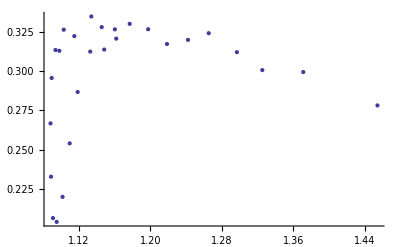

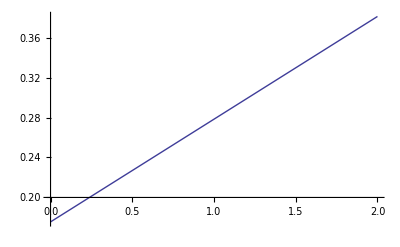

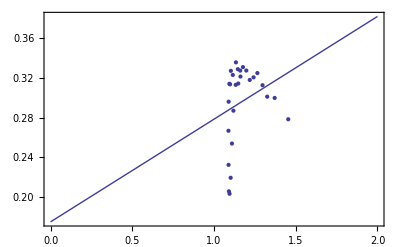

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```